## Setup

```mathematica
R=10;
n=11;
h=R/(n-1);
```

```mathematica
symm[i_]=If[i>=1,i,2-i];
```

```mathematica
(grad2=1/h Table[
(If[j==symm[i-1],-1,0]+
If[j==symm[i+1],+1,0])/2,
{i,n},{j,n}])//MatrixForm;
grad2[[n,n]]=1;
grad2[[n,n-1]]=-1;
grad2//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1/2 | 0 | 1/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 1/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 1/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 1/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 1/2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1)

```mathematica
(grad4=1/h Table[
(If[j==symm[i-2],+1,0]+
If[j==symm[i-1],-8,0]+
If[j==symm[i+1],+8,0]+
If[j==symm[i+2],-1,0])/12,
{i,n},{j,n}])//MatrixForm;
grad4[[n,n]]=3/2;grad4[[n,n-1]]=-2;grad4[[n,n-2]]=1/2;
grad4[[n-1,n]]=1/2;grad4[[n-1,n-1]]=0;grad4[[n-1,n-2]]=-1/2;grad4[[n-1,n-3]]=0;
grad4//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2/3 | 1/12 | 2/3 | -1/12 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/12 | -2/3 | 0 | 2/3 | -1/12 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/12 | -2/3 | 0 | 2/3 | -1/12 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/12 | -2/3 | 0 | 2/3 | -1/12 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/12 | -2/3 | 0 | 2/3 | -1/12 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/12 | -2/3 | 0 | 2/3 | -1/12 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/12 | -2/3 | 0 | 2/3 | -1/12 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/12 | -2/3 | 0 | 2/3 | -1/12
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 1/2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | -2 | 3/2)

```mathematica
(grad6=1/h Table[
(If[j==symm[i-3],-1,0]+
If[j==symm[i-2],+9,0]+
If[j==symm[i-1],-180/4,0]+
If[j==symm[i+1],180/4,0]+
If[j==symm[i+2],-9,0]+
If[j==symm[i+3],+1,0])/60,
{i,n},{j,n}])//MatrixForm;
```

```mathematica
(grad8=1/h Table[
(     If[j==symm[i-4],+1,0]+
If[j==symm[i-3],-(280*4)/105,0]+
If[j==symm[i-2],+280/5,0]+
If[j==symm[i-1],-280*4/5,0]+
If[j==symm[i+1],+280*4/5,0]+
If[j==symm[i+2],-280/5,0]+
If[j==symm[i+3],+(280*4)/105,0]+
If[j==symm[i+4],-1,0])/280,
{i,n},{j,n}])//MatrixForm;
```

```mathematica
(W=h DiagonalMatrix[Table[
If[i==1||i==n,1/2,1],
{i,n}]])//MatrixForm;
```

```mathematica
(B=DiagonalMatrix[Table[0,{i,n}]])//MatrixForm;
B[[n,n]]=1;
(*B[[1,1]]=-1;*)
B//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
QV=DiagonalMatrix[Table[q[i],{i,n}]];
```

```mathematica
(div2=Inverse[W].Transpose[B-W.grad2])//MatrixForm;
(div4=Inverse[W].Transpose[B-W.grad4])//MatrixForm;
(div6=Inverse[W].Transpose[B-W.grad6])//MatrixForm;
(div8=Inverse[W].Transpose[B-W.grad8])//MatrixForm;
```

```mathematica
(c=Table[1,{i,n}])//MatrixForm;
```

```mathematica
(r=h Table[i-1,{i,n}])//MatrixForm;
div2.r-1
div4.r^3-3 r^2
div6.r
div8.r
grad2.r^2-2r
grad4.r^4-4 r^3
grad6.r^2-2r
grad8.r^2-2r
```

{0,0,0,0,0,0,0,0,0,0,0}

{0,0,0,0,0,0,0,243/4,-1729/6,1777/4,-1331/3}

{1,1,1,1,1,1,1,11/12,47/30,-13/10,26/3}

{1,1,1,1,1,1,57/56,713/840,341/210,-339/280,349/42}

{0,0,0,0,0,0,0,0,0,0,-1}

{0,0,0,0,0,0,0,0,0,36,-74}

{0,0,0,0,0,0,0,0,-121/60,63/4,-2159/30}

{0,0,0,0,0,0,0,121/280,-86/21,5409/280,-3097/42}

## 2nd Order

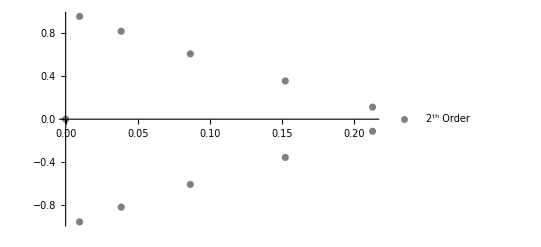

```mathematica
(cond2=div2.QV.r-3QV.c)//MatrixForm;
cond22=Join[cond2[[1;;-2]],{q[n]-r[[n]]^2}];
(sol2=Solve[cond22==0,Table[q[i],{i,n}]][[1]])//MatrixForm;
QQV2=QV/.sol2;
DDIV2=Inverse[QQV2].div2.QQV2;
DDIV2.r//FullSimplify;
(vals2=Eigenvalues[DDIV2])//N//MatrixForm;
cplot2=ComplexListPlot[vals2,AspectRatio->1/GoldenRatio,PlotStyle->Gray,PlotLegends->{"2^th Order"}]
```

## 4th Order

```mathematica
order=3;
```

```mathematica
(QS4= QV
+Table[Which[i≤order&&j≤order,
Which[
j>i,q[i,j],
j<i,q[j,i],
True,0],
True,0],{i,n},{j,n}]
)//MatrixForm
```

(q[1] | q[1,2] | q[1,3] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
q[1,2] | q[2] | q[2,3] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
q[1,3] | q[2,3] | q[3] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | q[4] | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | q[5] | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | q[6] | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | q[7] | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | q[8] | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | q[9] | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | q[10] | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | q[11])

```mathematica
(cond4a=div4.QV.r-3QS4.c)//MatrixForm;
(cond4b=div4.QV.r^3-5QS4.r^2)//MatrixForm;
```

```mathematica
(cond4=Join[
cond4a[[;;-3]],
cond4b[[;;3]],
{q[n-1]-r[[n-1]]^2,
q[n]-r[[n]]^2}])//MatrixForm;
(vars4 = DeleteDuplicates[SparseArray[QS4]["NonzeroValues"]])//MatrixForm;
(*RealQ[x_]:=!(Element[x,Reals]===True)
vars =Select[vars,RealQ];*)
Length[vars4];
Length[cond4];
```

```mathematica
(solq4=Solve[cond4==0,vars4][[1]])//MatrixForm//N
```

(q[1.]→0.723405
q[1.,2.]→-0.506583
q[1.,3.]→0.111679
q[2.]→1.06034
q[2.,3.]→-0.255845
q[3.]→1.28484
q[4.]→2.92416
q[5.]→5.15819
q[6.]→8.05901
q[7.]→11.5093
q[8.]→15.1472
q[9.]→16.5226
q[10.]→81.
q[11.]→100.)

```mathematica
(QQS4 = QS4/.solq4)//MatrixForm//N;
QQV4=QV/.solq4;
```

```mathematica
PositiveDefiniteMatrixQ[QQS4]
```

True

```mathematica
(DDIV4 = Inverse[QQS4].div4.QQV4)//N//MatrixForm;
```

```mathematica
DDIV4.r//FullSimplify//MatrixForm;
```

```mathematica
(DDIV4.r^3-5 r^2)[[;;3]]//FullSimplify//MatrixForm
```

(0
0
0)

```mathematica
(vals4=Eigenvalues[N[DDIV4]])//MatrixForm
```

(0.0436559+1.29816 ⅈ
0.0436559-1.29816 ⅈ
0.143454+1.17015 ⅈ
0.143454-1.17015 ⅈ
0.153325+0.901781 ⅈ
0.153325-0.901781 ⅈ
0.20287+0.498629 ⅈ
0.20287-0.498629 ⅈ
0.41302+0. ⅈ
0.307053+0. ⅈ
0.+0. ⅈ)

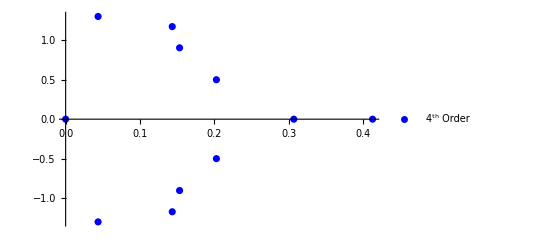

```mathematica
cplot4=ComplexListPlot[vals4,AspectRatio->1/GoldenRatio, PlotStyle->Blue, PlotLegends->{"4^th Order"}]
```

## 6th Order

```mathematica
order=5;
(QS6= QV
+Table[Which[i≤order&&j≤order,
Which[
j>i+1,q[i,j],
j<i-1,q[j,i],
True,0],
True,0],{i,n},{j,n}]
+Table[If[i≤n-3&& j≤n-3,Which[j==i+1,q[i,j],j==i-1,q[j,i],True,0],0],{i,n},{j,n}]
)//MatrixForm
```

(q[1] | q[1,2] | q[1,3] | q[1,4] | q[1,5] | 0 | 0 | 0 | 0 | 0 | 0
q[1,2] | q[2] | q[2,3] | q[2,4] | q[2,5] | 0 | 0 | 0 | 0 | 0 | 0
q[1,3] | q[2,3] | q[3] | q[3,4] | q[3,5] | 0 | 0 | 0 | 0 | 0 | 0
q[1,4] | q[2,4] | q[3,4] | q[4] | q[4,5] | 0 | 0 | 0 | 0 | 0 | 0
q[1,5] | q[2,5] | q[3,5] | q[4,5] | q[5] | q[5,6] | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | q[5,6] | q[6] | q[6,7] | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | q[6,7] | q[7] | q[7,8] | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | q[7,8] | q[8] | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | q[9] | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | q[10] | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | q[11])

```mathematica
(cond6a=div6.QV.r-3QS6.c)//MatrixForm;
(cond6b=div6.QV.r^3-5QS6.r^2)//MatrixForm;
(cond6c=div6.QV.r^5-7QS6.r^4)//MatrixForm;
```

```mathematica
(cond6=Join[
cond6a[[;;-4]],
cond6b[[;;-4]],
cond6c[[;;5]],
{q[n-2]-r[[n-2]]^2,
q[n-1]-r[[n-1]]^2,
q[n]-r[[n]]^2}])//MatrixForm;
(vars6 = DeleteDuplicates[SparseArray[QS6]["NonzeroValues"]])//MatrixForm;
(*RealQ[x_]:=!(Element[x,Reals]===True)
vars =Select[vars,RealQ];*)
Length[vars6]
Length[cond6]
```

24

24

```mathematica
(solq6=Solve[cond6==0,vars6][[1]])//MatrixForm//N
```

(q[1.]→-624.586
q[1.,2.]→459.23
q[1.,3.]→102.869
q[1.,4.]→-236.883
q[1.,5.]→65.2373
q[2.]→-383.998
q[2.,3.]→-129.836
q[2.,4.]→248.191
q[2.,5.]→-65.6519
q[3.]→208.798
q[3.,4.]→-123.756
q[3.,5.]→24.9253
q[4.]→-11.2102
q[4.,5.]→11.3322
q[5.]→15.1017
q[5.,6.]→-3.46392
q[6.]→20.2378
q[6.,7.]→5.79864
q[7.]→36.9204
q[7.,8.]→-3.61261
q[8.]→47.2837
q[9.]→64.
q[10.]→81.
q[11.]→100.)

```mathematica
(QQS6 = QS6/.solq6)//MatrixForm//N
QQV6=QV/.solq6;
```

(-624.586 | 459.23 | 102.869 | -236.883 | 65.2373 | 0. | 0. | 0. | 0. | 0. | 0.
459.23 | -383.998 | -129.836 | 248.191 | -65.6519 | 0. | 0. | 0. | 0. | 0. | 0.
102.869 | -129.836 | 208.798 | -123.756 | 24.9253 | 0. | 0. | 0. | 0. | 0. | 0.
-236.883 | 248.191 | -123.756 | -11.2102 | 11.3322 | 0. | 0. | 0. | 0. | 0. | 0.
65.2373 | -65.6519 | 24.9253 | 11.3322 | 15.1017 | -3.46392 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | -3.46392 | 20.2378 | 5.79864 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 5.79864 | 36.9204 | -3.61261 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | -3.61261 | 47.2837 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 64. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 81. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 100.)

```mathematica
PositiveDefiniteMatrixQ[QQS6]
```

False

```mathematica
(DDIV6 = Inverse[QQS6].div6.QQV6)//N//MatrixForm;
```

```mathematica
DDIV6.r//FullSimplify//MatrixForm//N
```

(3.
3.
3.
3.
3.
3.
3.
3.
3.9852
0.456245
10.4907)

```mathematica
(DDIV6.r^3-5 r^2)//FullSimplify//MatrixForm//N
```

(0.
0.
0.
0.
0.
0.
0.
0.
82.7669
-217.051
707.163)

```mathematica
(DDIV6.r^5-7 r^4)//FullSimplify//MatrixForm//N
```

(-5.65463
-11.8166
-22.3288
-63.4025
-165.967
-974.196
543.564
-577.335
7003.22
-17636.2
64282.)

```mathematica
(vals6=Eigenvalues[N[DDIV6]])//MatrixForm
```

(2.62748+1.40911 ⅈ
2.62748-1.40911 ⅈ
1.71061+0. ⅈ
0.00607795+1.4302 ⅈ
0.00607795-1.4302 ⅈ
0.0823826+0.918494 ⅈ
0.0823826-0.918494 ⅈ
0.143983+0.309103 ⅈ
0.143983-0.309103 ⅈ
0.0955129+0. ⅈ
0.+0. ⅈ)

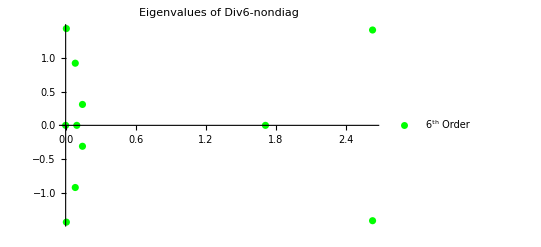

```mathematica
cplot6=ComplexListPlot[vals6,AspectRatio->1/GoldenRatio,PlotRange->All, PlotLabel->"Eigenvalues of Div6-nondiag",PlotStyle->Green,PlotLegends->{"6^th Order"}]
```

## 8th Order

```mathematica
order=6;
(QS8= QV
+Table[Which[i≤order&&j≤order,
Which[
j>i+2,q[i,j],
j<i-2,q[j,i],
True,0],
True,0],{i,n},{j,n}]
+Table[If[i≤n-4&& j≤n-4,Which[j==i+1,q[i,j],j==i-1,q[j,i],True,0],0],{i,n},{j,n}]
+Table[If[i≤n-4&& j≤n-4,Which[j==i+2,q[i,j],j==i-2,q[j,i],True,0],0],{i,n},{j,n}]
)//MatrixForm
```

(q[1] | q[1,2] | q[1,3] | q[1,4] | q[1,5] | q[1,6] | 0 | 0 | 0 | 0 | 0
q[1,2] | q[2] | q[2,3] | q[2,4] | q[2,5] | q[2,6] | 0 | 0 | 0 | 0 | 0
q[1,3] | q[2,3] | q[3] | q[3,4] | q[3,5] | q[3,6] | 0 | 0 | 0 | 0 | 0
q[1,4] | q[2,4] | q[3,4] | q[4] | q[4,5] | q[4,6] | 0 | 0 | 0 | 0 | 0
q[1,5] | q[2,5] | q[3,5] | q[4,5] | q[5] | q[5,6] | q[5,7] | 0 | 0 | 0 | 0
q[1,6] | q[2,6] | q[3,6] | q[4,6] | q[5,6] | q[6] | q[6,7] | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | q[5,7] | q[6,7] | q[7] | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | q[8] | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | q[9] | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | q[10] | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | q[11])

```mathematica
(*QS8=({{q[1], q[1,2], q[1,3], q[1,4], q[1,5], q[1,6], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {q[1,2], q[2], q[2,3], q[2,4], q[2,5], q[2,6], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {q[1,3], q[2,3], q[3], q[3,4], q[3,5], q[3,6], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {q[1,4], q[2,4], q[3,4], q[4], q[4,5], q[4,6], q[4,7], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {q[1,5], q[2,5], q[3,5], q[4,5], q[5], q[5,6], q[5,7], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {q[1,6], q[2,6], q[3,6], q[4,6], q[5,6], q[6], q[6,7], q[6,8], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, q[4,7], q[5,7], q[6,7], q[7], q[7,8], q[7,9], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, q[6,8], q[7,8], q[8], q[8,9], q[8,10], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, q[7,9], q[8,9], q[9], q[9,10], q[9,11], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, q[8,10], q[9,10], q[10], q[10,11], q[10,12], 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, q[9,11], q[10,11], q[11], q[11,12], q[11,13], 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, q[10,12], q[11,12], q[12], q[12,13], q[12,14], 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, q[11,13], q[12,13], q[13], q[13,14], q[13,15], 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, q[12,14], q[13,14], q[14], q[14,15], q[14,16], 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, q[13,15], q[14,15], q[15], q[15,16], q[15,17], 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, q[14,16], q[15,16], q[16], q[16,17], 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, q[15,17], q[16,17], q[17], 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, q[18], 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, q[19], 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, q[20], 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, q[21]}})*)
```

```mathematica
(cond8a=div8.QV.r^1-3QS8.c)//MatrixForm;
(cond8b=div8.QV.r^3-5QS8.r^2)//MatrixForm;
(cond8c=div8.QV.r^5-7QS8.r^4)//MatrixForm;
(cond8d=div8.QV.r^7-9QS8.r^6)//MatrixForm;
```

```mathematica
G[q1_]:=
Module[{u},
cond8G=Join[
cond8a[[;;-5]],
cond8b[[;;-5]],
cond8c[[;;-5]],
cond8d[[;;4]],
{q[1]-q1,
q[n-1]-r[[n-1]]^2,
q[n]-r[[n]]^2}
];vars8G = DeleteDuplicates[SparseArray[QS8]["NonzeroValues"]];solq8G=Solve[cond8G==0,vars8G][[1]];QQS8G = QS8/.solq8G;QQV8G=QV/.solq8G;DDIV8G= N[Inverse[QQS8G].div8.QQV8G];((DDIV8G.r^7-9.0 r^6)[[1]])^2]
```

```mathematica
(*q1sol=NMinimize[{G[k],k≥0.0,k≤1},k]*)
```

```mathematica
(*FindMinimum[{G[k],k≥0.0,k≤1},{k,100419445/108274511 h^2}]*)
```

```mathematica
(*q10=q1sol[[2]][[1]]// Values;*)
```

```mathematica
(*q1Rational = Rationalize[N[q10],10^-16]*)
```

```mathematica
(cond8=Join[
cond8a[[;;-5]],
cond8b[[;;-5]],
cond8c[[;;-5]],
cond8d[[;;4]],
{(*q[1]-2045027588481283/2251799813685248,*)
(*q[1]-q1Rational,*)
q[1]-h^2,
(*q[n-2]-r[[n-2]]^2,*)
q[n-1]-r[[n-1]]^2,
q[n]-r[[n]]^2}
])//MatrixForm;
(vars8 = DeleteDuplicates[SparseArray[QS8]["NonzeroValues"]])//MatrixForm;
Length[vars8]
Length[cond8]
```

28

28

```mathematica
(solq8=Solve[cond8==0,vars8][[1]])//MatrixForm//N
```

(q[1.]→1.
q[1.,2.]→-0.74383
q[1.,3.]→0.819887
q[1.,4.]→-0.451361
q[1.,5.]→0.18134
q[1.,6.]→-0.0358798
q[2.]→2.71904
q[2.,3.]→-1.32005
q[2.,4.]→0.684345
q[2.,5.]→-0.154941
q[2.,6.]→0.0104375
q[3.]→5.21669
q[3.,4.]→0.33568
q[3.,5.]→-0.204958
q[3.,6.]→0.0229828
q[4.]→12.1258
q[4.,5.]→0.319223
q[4.,6.]→-0.0373133
q[5.]→22.3386
q[5.,6.]→-0.536517
q[5.,7.]→0.23265
q[6.]→34.3817
q[6.,7.]→0.0315106
q[7.]→49.4777
q[8.]→66.7793
q[9.]→81.0747
q[10.]→81.
q[11.]→100.)

```mathematica
(QQS8 = QS8/.solq8)//MatrixForm//N
QQV8=QV/.solq8;
```

(1. | -0.74383 | 0.819887 | -0.451361 | 0.18134 | -0.0358798 | 0. | 0. | 0. | 0. | 0.
-0.74383 | 2.71904 | -1.32005 | 0.684345 | -0.154941 | 0.0104375 | 0. | 0. | 0. | 0. | 0.
0.819887 | -1.32005 | 5.21669 | 0.33568 | -0.204958 | 0.0229828 | 0. | 0. | 0. | 0. | 0.
-0.451361 | 0.684345 | 0.33568 | 12.1258 | 0.319223 | -0.0373133 | 0. | 0. | 0. | 0. | 0.
0.18134 | -0.154941 | -0.204958 | 0.319223 | 22.3386 | -0.536517 | 0.23265 | 0. | 0. | 0. | 0.
-0.0358798 | 0.0104375 | 0.0229828 | -0.0373133 | -0.536517 | 34.3817 | 0.0315106 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.23265 | 0.0315106 | 49.4777 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 66.7793 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 81.0747 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 81. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 100.)

```mathematica
PositiveDefiniteMatrixQ[QQS8]
```

True

```mathematica
DDIV8= Inverse[QQS8].div8.QQV8;
```

```mathematica
DDIV8.r//FullSimplify//MatrixForm//N
```

(3.
3.
3.
3.
3.
3.
3.
2.78141
2.00284
-0.445461
10.5954)

```mathematica
DDIV8.r^3-5 r^2//FullSimplify//MatrixForm//N
```

(0.
0.
0.
0.
0.
0.
0.
-11.9986
-62.2897
-269.431
704.569)

```mathematica
DDIV8.r^5-7 r^4//FullSimplify//MatrixForm//N
```

(0.
0.
0.
0.
0.
0.
0.
-753.455
-3985.82
-20187.8
63271.5)

```mathematica
DDIV8.r^7-9 r^6//MatrixForm//N
```

(105.193
1.13092
-27.7359
12.0153
-79.9669
1719.26
1998.03
-55128.3
-279621.
-1.39457×10^6
5.44046×10^6)

```mathematica
(vals8=Eigenvalues[N[DDIV8]])//MatrixForm
```

(0.254661+1.72548 ⅈ
0.254661-1.72548 ⅈ
1.66477+0. ⅈ
0.119171+1.53286 ⅈ
0.119171-1.53286 ⅈ
0.186054+1.05744 ⅈ
0.186054-1.05744 ⅈ
0.21311+0.535219 ⅈ
0.21311-0.535219 ⅈ
0.224855+0. ⅈ
0.+0. ⅈ)

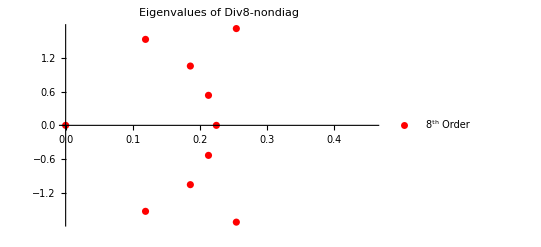

```mathematica
cplot8=ComplexListPlot[vals8,AspectRatio->1/GoldenRatio,PlotRange->Automatic,PlotLabel->"Eigenvalues of Div8-nondiag",PlotStyle->Red,PlotLegends->{"8^th Order"}]
```

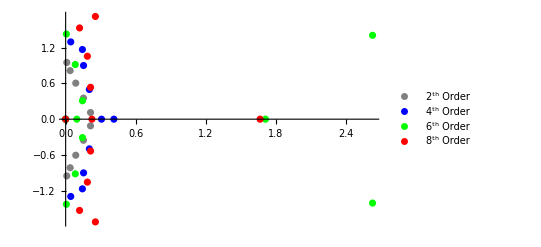

```mathematica
Show[cplot2, cplot4, cplot6, cplot8, AspectRatio->1/GoldenRatio,PlotRange->All]
```

```mathematica
(lvals8=Sort[Eigenvalues[DDIV8.grad8]])//MatrixForm
(lvals6=Sort[Eigenvalues[DDIV6.grad6]])//MatrixForm
(lvals4=Sort[Eigenvalues[DDIV4.grad4]])//MatrixForm
(lvals2=Sort[Eigenvalues[DDIV2.grad2]])//MatrixForm
```

(0
Root-6.86Root[«1»&,1]-6.857850884791475
Root-2.83Root[«1»&,2]-2.8293136924668185
Root-2.73Root[«1»&,3]-2.730662514951271
Root-2.06Root[«1»&,4]-2.0550433282439444
Root-1.93Root[«1»&,5]-1.9329543428396
Root-1.41Root[«1»&,6]-1.4081990134502584
Root-0.313Root[«1»&,7]-0.3129394124257206
Root-2.97 × 10^-3Root[«1»&,8]-0.0029730367046372727
Root-0.878-0.0690 ⅈRoot[«1»&,9]-0.877612451030175
Root-0.878+0.0690 ⅈRoot[«1»&,10]-0.877612451030175)

(0
Root-2.74Root[«1»&,1]-2.7374456814617454
Root-0.759Root[«1»&,2]-0.758647781982741
Root-0.0610Root[«1»&,3]-0.06096899540830222
Root0.194Root[«1»&,4]0.194348144346636
Root-1.71-0.153 ⅈRoot[«1»&,5]-1.705507308350008
Root-1.71+0.153 ⅈRoot[«1»&,6]-1.705507308350008
Root-0.671-0.833 ⅈRoot[«1»&,7]-0.6709602901213821
Root-0.671+0.833 ⅈRoot[«1»&,8]-0.6709602901213821
Root-0.261-0.0917 ⅈRoot[«1»&,9]-0.2606609728035409
Root-0.261+0.0917 ⅈRoot[«1»&,10]-0.2606609728035409)

(0
Root-3.07Root[«1»&,1]-3.0736713046049413
Root-2.66Root[«1»&,2]-2.6600977412446953
Root-1.76Root[«1»&,3]-1.7570057075158683
Root-1.04Root[«1»&,4]-1.0444476765249804
Root-0.678Root[«1»&,5]-0.6776240612908743
Root-0.496Root[«1»&,6]-0.4959079927298067
Root-0.253Root[«1»&,7]-0.25254690720540146
Root-0.154Root[«1»&,8]-0.15362260867657437
Root-1.51-0.0670 ⅈRoot[«1»&,9]-1.5136382719880284
Root-1.51+0.0670 ⅈRoot[«1»&,10]-1.5136382719880284)

(0
Root-1.63Root[3255726309352110+180692810169042105 #1+3534930069649703406 #1^2+«6»+265219580426191699968 #1^9+42673455881939976192 #1^10&,1]-1.6319119079942994
Root-1.04Root[3255726309352110+180692810169042105 #1+3534930069649703406 #1^2+«6»+265219580426191699968 #1^9+42673455881939976192 #1^10&,2]-1.0431644389204868
Root-0.927Root[3255726309352110+180692810169042105 #1+3534930069649703406 #1^2+«6»+265219580426191699968 #1^9+42673455881939976192 #1^10&,3]-0.9272177496394844
Root-0.813Root[3255726309352110+180692810169042105 #1+3534930069649703406 #1^2+«6»+265219580426191699968 #1^9+42673455881939976192 #1^10&,4]-0.812958939711335
Root-0.655Root[3255726309352110+180692810169042105 #1+3534930069649703406 #1^2+«6»+265219580426191699968 #1^9+42673455881939976192 #1^10&,5]-0.6545412587071859
Root-0.502Root[3255726309352110+180692810169042105 #1+3534930069649703406 #1^2+«6»+265219580426191699968 #1^9+42673455881939976192 #1^10&,6]-0.5022398344875302
Root-0.330Root[3255726309352110+180692810169042105 #1+3534930069649703406 #1^2+«6»+265219580426191699968 #1^9+42673455881939976192 #1^10&,7]-0.3303458085851289
Root-0.206Root[3255726309352110+180692810169042105 #1+3534930069649703406 #1^2+«6»+265219580426191699968 #1^9+42673455881939976192 #1^10&,8]-0.20567447252490242
Root-0.0678Root[3255726309352110+180692810169042105 #1+3534930069649703406 #1^2+«6»+265219580426191699968 #1^9+42673455881939976192 #1^10&,9]-0.06775096851099045
Root-0.0393Root[3255726309352110+180692810169042105 #1+3534930069649703406 #1^2+«6»+265219580426191699968 #1^9+42673455881939976192 #1^10&,10]-0.03928957736994445)

```mathematica
k=Table[i π/R,{i,1,n}];
λ=-k^2;
```

```mathematica
plot0=Plot[λ,{x,.2,1},PlotStyle->Red,Axes->{False,True},AspectRatio->GoldenRatio,PlotRange->{{0,1},Automatic}];
```

```mathematica
plot8=Plot[lvals8,{x,.2,1},PlotStyle->Black,Axes->{False,True},AspectRatio->GoldenRatio,PlotRange->{{0,1},Automatic}];
```

```mathematica
plot6=Plot[lvals6,{x,.2,1},PlotStyle->Black,Axes->{False,True},AspectRatio->GoldenRatio,PlotRange->{{0,1},Automatic}];
```

```mathematica
plot4=plot4s=Plot[lvals4,{x,.2,1},PlotStyle->Black,Axes->{False,True},AspectRatio->GoldenRatio,PlotRange->{{0,1},Automatic}];
```

```mathematica
(cvals4=Eigenvalues[div4.grad4]) // MatrixForm//N;
```

```mathematica
plot2=Plot[lvals2,{x,.2,1},PlotStyle->Black,Axes->{False,True},AspectRatio->GoldenRatio,PlotRange->{{0,1},Automatic}];
```

```mathematica
plot4c=Plot[cvals4,{x,.2,1},PlotStyle->Blue,Axes->{False,True},AspectRatio->GoldenRatio,PlotRange->{{0,1},Automatic}];
```

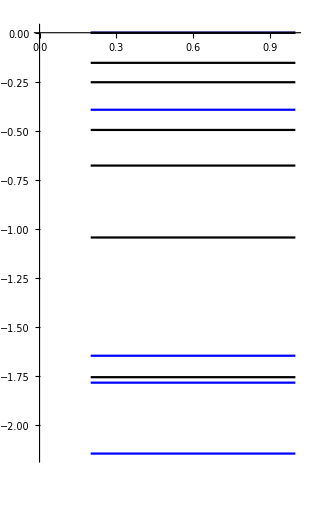

```mathematica
Show[plot4c,plot4s]
```

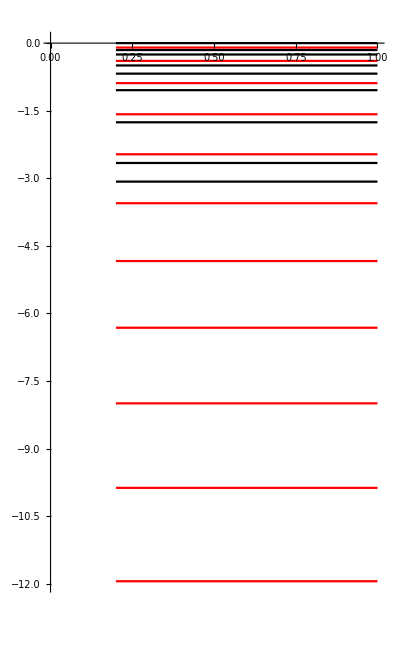

```mathematica
Show[plot0,plot4]
```

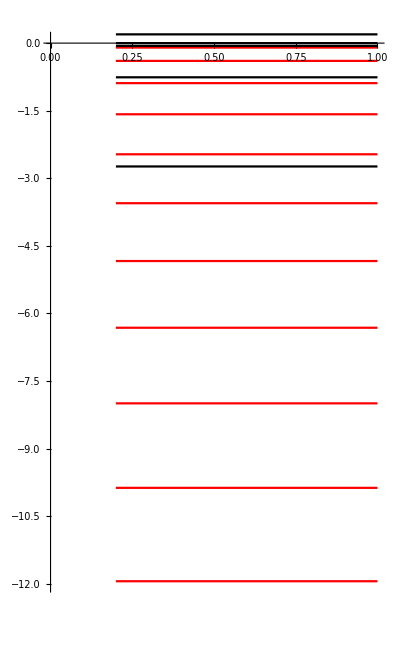

```mathematica
Show[plot0, plot6]
```

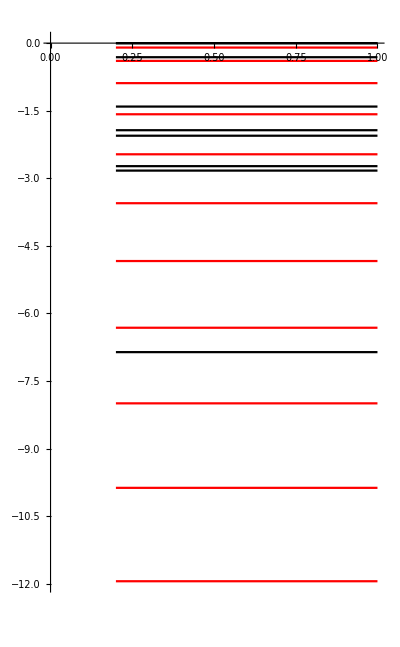

```mathematica
Show[plot0, plot8]
```

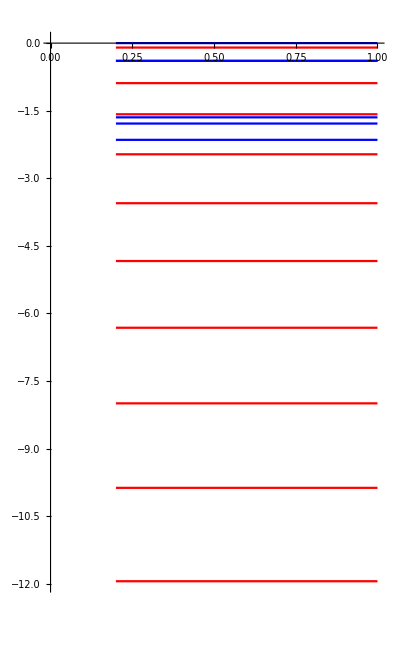

```mathematica
Show[plot0, plot4c]
```

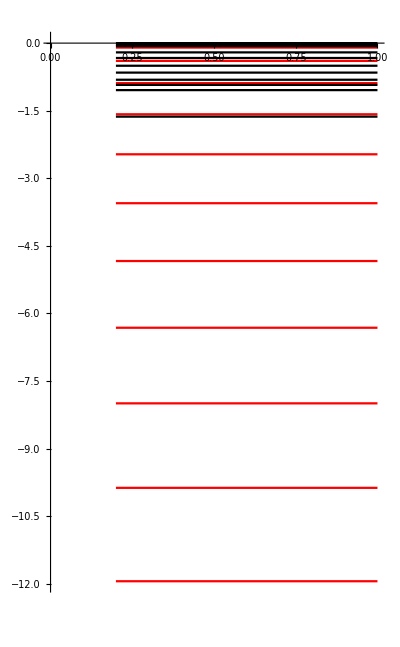

```mathematica
Show[plot0,plot2]
```

```mathematica
(vecs2=Eigenvectors[N[DDIV2.grad2]])//MatrixForm;
```

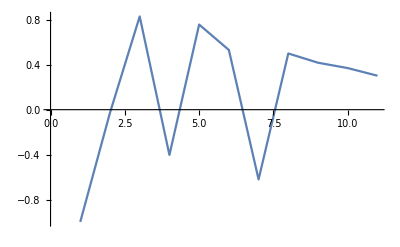

```mathematica
ListLinePlot[vecs2[[;;,1]]]
```